```mathematica
fishdat=Import["/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/FISH_data/table_15_0003.csv","Data"];
egfrdat=Table[{fishdat[[i]][[2]],fishdat[[i]][[3]],fishdat[[i]][[4]]},{i,2,Length[fishdat]}];
pdgfradat=Table[{fishdat[[i]][[2]],fishdat[[i]][[3]],fishdat[[i]][[5]]},{i,2,Length[fishdat]}];
cdk4dat=Table[{fishdat[[i]][[2]],fishdat[[i]][[3]],fishdat[[i]][[6]]},{i,2,Length[fishdat]}];
egfrdat2={};
For[i=1,i≤Length[egfrdat],i++,
thispoint=If[ egfrdat[[i]][[3]]≥6,{egfrdat[[i]][[1]],egfrdat[[i]][[2]],1},{egfrdat[[i]][[1]],egfrdat[[i]][[2]],0}];
AppendTo[egfrdat2,thispoint]]
cdk4dat2={};
For[i=1,i≤Length[cdk4dat],i++,
thispoint=If[ cdk4dat[[i]][[3]]≥6,{cdk4dat[[i]][[1]],cdk4dat[[i]][[2]],1},{cdk4dat[[i]][[1]],cdk4dat[[i]][[2]],0}];
AppendTo[cdk4dat2,thispoint]]
pdgfradat2={};
For[i=1,i≤Length[pdgfradat],i++,
thispoint=If[ pdgfradat[[i]][[3]]≥6,{pdgfradat[[i]][[1]],pdgfradat[[i]][[2]],1},{pdgfradat[[i]][[1]],pdgfradat[[i]][[2]],0}];
AppendTo[pdgfradat2,thispoint]]
Length[fishdat]
```

398

223.

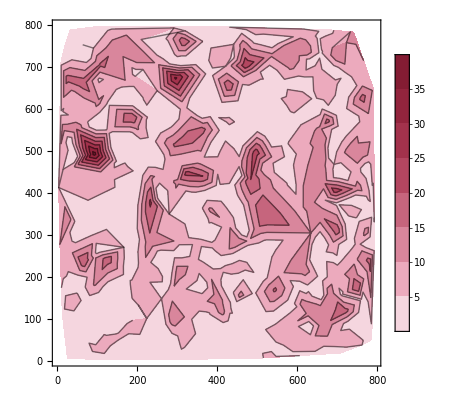

```mathematica
egfr3d=ListContourPlot[egfrdat,PlotRange->All,PlotLegends->Automatic,ColorFunction->ColorData[{"ValentineTones","Reverse"}]]
```

```mathematica
Export["/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/egfrcopynumsSample.pdf",egfr3d]
```

/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/egfrcopynumsSample.pdf

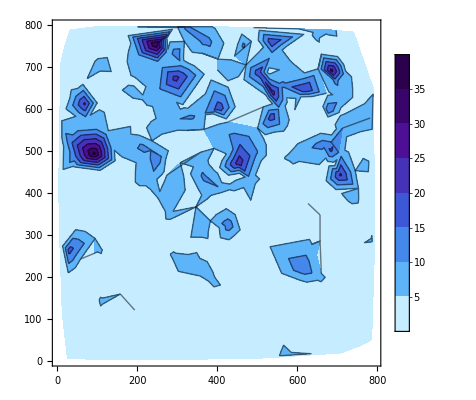

```mathematica
cdk3d=ListContourPlot[cdk4dat,PlotRange->All,PlotLegends->Automatic,ColorFunction->ColorData[{"DeepSeaColors","Reverse"}]]
```

```mathematica
Export["/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/cdk4copynumsSample.pdf",cdk3d]
```

/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/cdk4copynumsSample.pdf

```mathematica
buildHist[dat_]:=Module[{},
alldat={};
For[j=1,j≤Length[dat],j++,
datPointj=If[dat[[j]][[3]]>0,
Table[{dat[[j]][[1]],dat[[j]][[2]]},{totnum,1,dat[[j]][[3]]}],{}];
AppendTo[alldat,datPointj]];
Return[Flatten[alldat,1]/.{}->Nothing]]
```

```mathematica
skdEGFRbounded=SmoothKernelDistribution[buildHist[egfrdat],Automatic,{"Bounded",{{0,800},{0,800}},"Gaussian"}]
```

DataDistribution[…]

```mathematica
skdEGFRUnbounded=SmoothKernelDistribution[buildHist[egfrdat]]
```

DataDistribution[…]

```mathematica
skdCDKbounded=SmoothKernelDistribution[buildHist[cdk4dat],Automatic,{"Bounded",{{0,800},{0,800}},"Gaussian"}]
```

DataDistribution[…]

```mathematica
skdCDKUnbounded=SmoothKernelDistribution[buildHist[cdk4dat]]
```

DataDistribution[…]

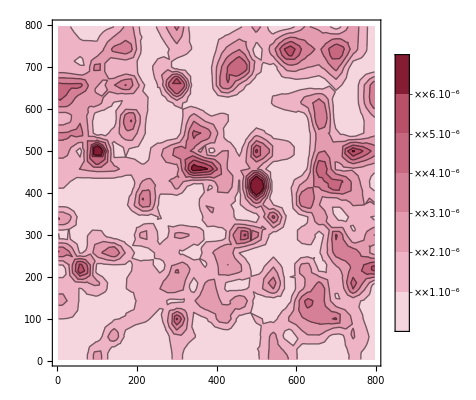

```mathematica
EGFRboundedCopyNumsPlt=ContourPlot[PDF[skdEGFRbounded,{x,y}],{x,0,800},{y,0,800},PlotRange->All,PlotLegends->Automatic,ColorFunction->ColorData[{"ValentineTones","Reverse"}]]
```

```mathematica
Export["/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/EGFRboundedCopyNumsPlt.pdf",EGFRboundedCopyNumsPlt]
```

/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/EGFRboundedCopyNumsPlt.pdf

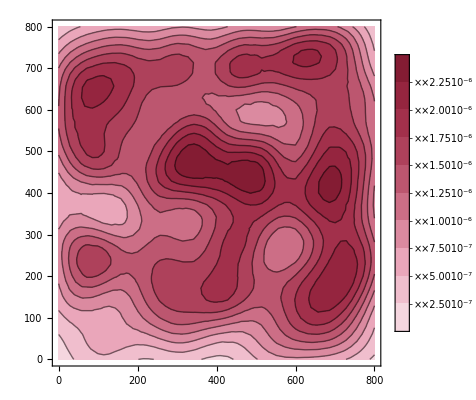

```mathematica
EGFRUnboundedCopyNumsPlt=ContourPlot[PDF[skdEGFRUnbounded,{x,y}],{x,0,800},{y,0,800},PlotRange->All,PlotLegends->Automatic,ColorFunction->ColorData[{"ValentineTones","Reverse"}]]
```

```mathematica
Export["/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/EGFRUnboundedCopyNumsPlt.pdf",EGFRUnboundedCopyNumsPlt]
```

/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/EGFRUnboundedCopyNumsPlt.pdf

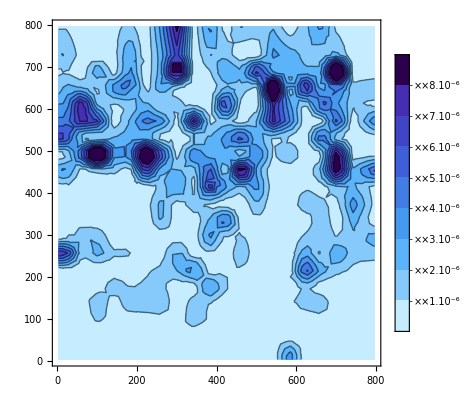

```mathematica
CDKboundedCopyNumsPlt=ContourPlot[PDF[skdCDKbounded,{x,y}],{x,0,800},{y,0,800},PlotRange->All,PlotLegends->Automatic,ColorFunction->ColorData[{"DeepSeaColors","Reverse"}]]
```

```mathematica
Export["/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/CDKboundedCopyNumsPlt.pdf",CDKboundedCopyNumsPlt]
```

/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/CDKboundedCopyNumsPlt.pdf

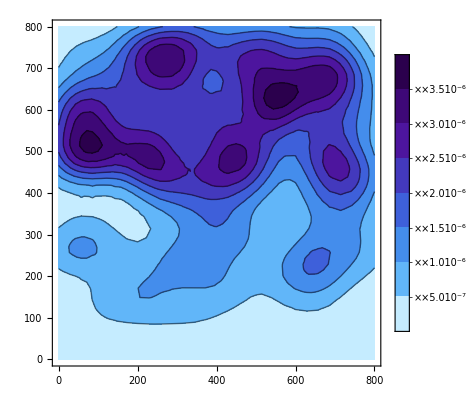

```mathematica
CDKUnboundedCopyNumsPlt=ContourPlot[PDF[skdCDKUnbounded,{x,y}],{x,0,800},{y,0,800},PlotRange->All,PlotLegends->Automatic,ColorFunction->ColorData[{"DeepSeaColors","Reverse"}]]
```

```mathematica
Export["/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/CDKUnboundedCopyNumsPlt.pdf",CDKUnboundedCopyNumsPlt]
```

/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/CDKUnboundedCopyNumsPlt.pdf

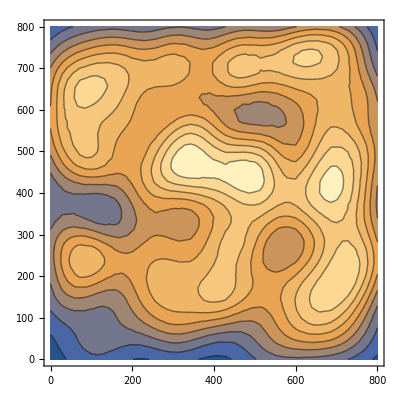

```mathematica
ContourPlot[PDF[skd1,{x,y}],{x,0,800},{y,0,800},PlotRange->All]
```

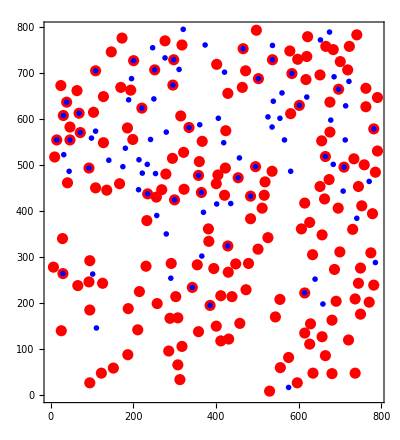

```mathematica
onesEGFR=Select[egfrdat2,#[[3]]>0&];
onesPDGFRA=Select[pdgfradat2,#[[3]]>0&];
onesCDK4=Select[cdk4dat2,#[[3]]>0&];
ListPlot[{Table[{onesEGFR[[i]][[1]],onesEGFR[[i]][[2]]},{i,1,Length[onesEGFR]}],Table[{onesCDK4[[i]][[1]],onesCDK4[[i]][[2]]},{i,1,Length[onesCDK4]}]},PlotStyle->{{Red,PointSize[0.02]},{Blue,PointSize[0.01]}},AspectRatio->1.1,Frame->True]
```

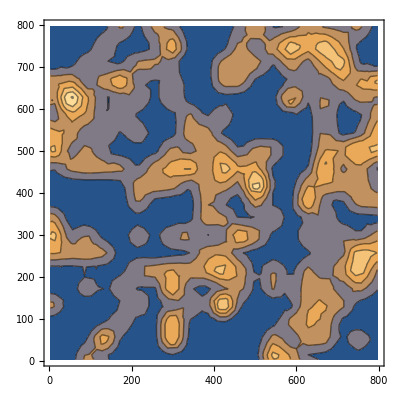

```mathematica
ContourPlot[PDF[skdB,{x,y}],{x,0,800},{y,0,800},PlotRange->All]
```

```mathematica
SmoothHistogram3D[Table[{onesEGFR[[i]][[1]],onesEGFR[[i]][[2]]},{i,1,Length[onesEGFR]}]]
```

-Graphics3D-

```mathematica
skdB=SmoothKernelDistribution[Table[{onesEGFR[[i]][[1]],onesEGFR[[i]][[2]]},{i,1,Length[onesEGFR]}],Automatic,{"Bounded",{{0,800},{0,800}},"Gaussian"}];
skdPDGFRAB=SmoothKernelDistribution[Table[{onesPDGFRA[[i]][[1]],onesPDGFRA[[i]][[2]]},{i,1,Length[onesPDGFRA]}],Automatic,{"Bounded",{{0,800},{0,800}},"Gaussian"}];
skdCDKB=SmoothKernelDistribution[Table[{onesCDK4[[i]][[1]],onesCDK4[[i]][[2]]},{i,1,Length[onesCDK4]}],Automatic,{"Bounded",{{0,800},{0,800}},"Gaussian"}];
skd=SmoothKernelDistribution[Table[{onesEGFR[[i]][[1]],onesEGFR[[i]][[2]]},{i,1,Length[onesEGFR]}]];
skdCDK=SmoothKernelDistribution[Table[{onesCDK4[[i]][[1]],onesCDK4[[i]][[2]]},{i,1,Length[onesCDK4]}]];
```

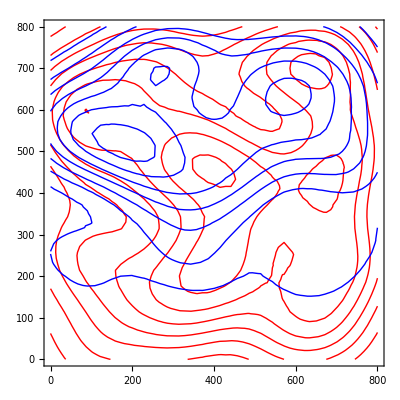

```mathematica
pltunbounded=Show[ContourPlot[PDF[skd,{x,y}],{x,0,800},{y,0,800},ContourShading->None,ContourStyle->Red],ContourPlot[PDF[skdCDK,{x,y}],{x,0,800},{y,0,800},ContourShading->None,ContourStyle->Blue,PlotRange->All]]
```

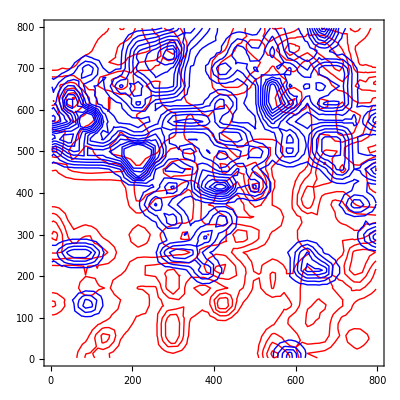

```mathematica
plt=Show[ContourPlot[PDF[skdB,{x,y}],{x,0,800},{y,0,800},ContourShading->None,ContourStyle->Red],ContourPlot[PDF[skdCDKB,{x,y}],{x,0,800},{y,0,800},ContourShading->None,ContourStyle->Blue,PlotRange->All]]
```

```mathematica
Export["/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/sample_contour_plot_unbounded.pdf",pltunbounded]
```

/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/sample_contour_plot_unbounded.pdf

```mathematica
onesPDGFRA
```

{{429,22,1},{426,45,1}}

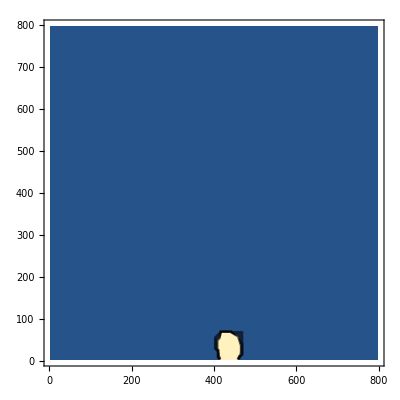

```mathematica
ContourPlot[PDF[skdPDGFRAB,{x,y}],{x,0,800},{y,0,800},PlotRange->All]
```

```mathematica
NIntegrate[Abs[PDF[skdCDKB,{x,y}]-PDF[skdPDGFRAB,{x,y}]],{x,0,800},{y,0,800},PrecisionGoal->4,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.99998

```mathematica
NIntegrate[Sqrt[PDF[skdCDKB,{x,y}]*PDF[skdPDGFRAB,{x,y}]],{x,0,800},{y,0,800},PrecisionGoal->4,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {461.779,45.3152}. NIntegrate obtained 1.5027×10^-7 and 1.04398×10^-10 for the integral and error estimates.

1.5027×10^-7

```mathematica
NIntegrate[Sqrt[PDF[skdCDKB,{x,y}]*PDF[skdPDGFRAB,{x,y}]],{x,0,800},{y,0,800},PrecisionGoal->3,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.50307×10^-7

```mathematica
Export["/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/sample_contour_plot.pdf",plt]
```

/Users/dalite/Dropbox (Partners HealthCare)/GBM_data_Sep3/sample_contour_plot.pdf

```mathematica
NIntegrate[Sqrt[PDF[skdB,{x,y}]*PDF[skdCDKB,{x,y}]],{x,0,800},{y,0,800}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.345605

```mathematica
1-NIntegrate[Sqrt[PDF[skdB,{x,y}]*PDF[skdCDKB,{x,y}]],{x,0,800},{y,0,800}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.654395

```mathematica
NIntegrate[Abs[PDF[skdB,{x,y}]-PDF[skdCDKB,{x,y}]],{x,0,800},{y,0,800}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.67343 and 0.0000115293 for the integral and error estimates.

1.67343

```mathematica
NIntegrate[Abs[PDF[skdB,{x,y}]-PDF[skdCDKB,{x,y}]],{x,0,800},{y,0,800},PrecisionGoal->5,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.67343

```mathematica
skdB
```

DataDistribution[…]

```mathematica
skdB[[2,3]]
```

{21.4566,21.4613}

```mathematica
Length[Table[{onesEGFR[[i]][[1]],onesEGFR[[i]][[2]]},{i,1,Length[onesEGFR]}]]
```

48

```mathematica
NIntegrate[Abs[SetPrecision[PDF[skdB,{x,y}],4]-SetPrecision[PDF[skdCDKB,{x,y}],4]],{x,0,800},{y,0,800},WorkingPrecision->1000,PrecisionGoal->3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.673466901400315858380453895047659890512475891691983317192068046204371125658024802108088931541971094655945771924944653036205103797378598544609843278701020748791372021744072313128565583577916702483853028652277665846221708509410098752765532368952422484241565220785709872431231192352985124785323238184068293424340733902875767129445824155794363823335853658998642256604088471232848577080837858688813790126617344992835513890551257123066221096747985920365000422842014677576588612268440889271474220384228375821194096154618346946905951180996170226865632885772089216410953382474426035942562790287725871295186683596690400580547817599791412949153752823693948371909777789890673446576141220522313268165007916114460652978694420921580441036542431434836535485250051366224892156182155246606817477710169592893222017933832634181448687244230535000058177006618023123254948483518307389063337598938902374779012610969559823802581515129368257578106478113458686149234902795316527661075301054579009867449715767613678017446909367

```mathematica
≥
```

```mathematica
1-NIntegrate[Abs[PDF[skd,{x,y}]-PDF[skdCDK,{x,y}]],{x,0,800},{y,0,800}]/2
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.883817 and 0.0000155899 for the integral and error estimates.

0.558092

```mathematica
skdEGFR=PDF[skd,{x,y}]/NIntegrate[PDF[skd,{x,y}],{x,0,800},{y,0,800}]
skdCDK4=PDF[skdCDK,{x,y}]/NIntegrate[PDF[skdCDK,{x,y}],{x,0,800},{y,0,800}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.913048 and 9.85947×10^-7 for the integral and error estimates.

1.09523 (Piecewise[{{0, x<-401.401||y<-280.614||x>1195.4||y>1123.61}, {InterpolatingFunction[…][x,y], True}}])

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.914136 and 1.42929×10^-6 for the integral and error estimates.

1.09393 (Piecewise[{{0, x<-360.75||y<-336.106||x>1154.75||y>1139.11}, {InterpolatingFunction[…][x,y], True}}])

```mathematica
NIntegrate[PDF[skdCDK4,{x,y}],{x,0,800},{y,0,800}]
```

NIntegrate::inumr: The integrand PDF[1.09393 (Piecewise[{{0, x<-360.75||y<-336.106||x>1154.75||y>1139.11}, {«1»[x,y], True}}]),{x,y}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,800},{0,800}}.

NIntegrate[PDF[skdCDK4,{x,y}],{x,0,800},{y,0,800}]

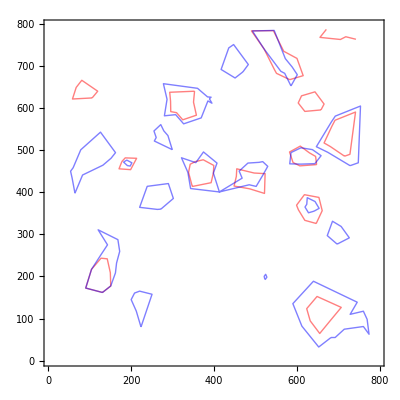

```mathematica
Show[ListContourPlot[egfrdat2,Contours->1,ContourShading->None,ContourStyle->Red],ListContourPlot[cdk4dat,Contours->1,ContourShading->None,ContourStyle->Blue]]
```

```mathematica
inttest=Interpolation[Table[{{egfrdat2[[i]][[1]],egfrdat2[[i]][[2]]},egfrdat2[[i]][[3]]},{i,1,Length[egfrdat2]}],InterpolationOrder->1]
inttest2=Interpolation[Table[{{cdk4dat[[i]][[1]],cdk4dat[[i]][[2]]},cdk4dat[[i]][[3]]},{i,1,Length[cdk4dat]}],InterpolationOrder->1]
```

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

InterpolatingFunction[…]

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

InterpolatingFunction[…]

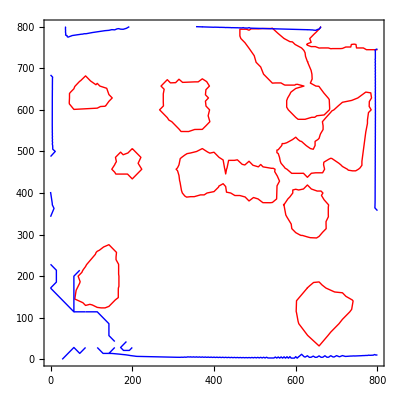

```mathematica
Show[ContourPlot[inttest[x,y],{x,0,800},{y,0,800},Contours->1,ContourShading->None,ContourStyle->Red],ContourPlot[inttest2[x,y],{x,0,800},{y,0,800},Contours->1,ContourShading->None,ContourStyle->Blue]]
```

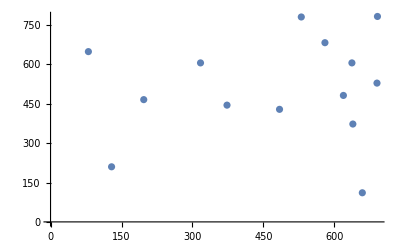

```mathematica
onesEGFR=Select[egfrdat2,#[[3]]>0&];
onesCDK4=Select[cdk4dat2,#[[3]]>0&];
ListPlot[Table[{onesEGFR[[i]][[1]],onesEGFR[[i]][[2]]},{i,1,Length[onesEGFR]}]]
```